```mathematica
Clear["Global`*"]
```

```mathematica
R={r,θ,ϕ};
X={x,y,z};
RealSphericalHarmonicY[l_,m_,θ_,ϕ_]:=If[m<0,
ⅉ/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]-(-1)^m SphericalHarmonicY[l,-m,θ,ϕ]),
If[m==0,
SphericalHarmonicY[l,m,θ,ϕ],
1/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]+(-1)^m SphericalHarmonicY[l,-m,θ,ϕ])
]
]
ψ[l_,m_]:=SphericalHankelH2[l,k r]SphericalHarmonicY[l,m,θ,ϕ]
(*Y[l_,m_]:={ψ[l,m],0,0};*)
Ψ[l_,m_]:=1/k Curl[Φ[l,m],R,"Spherical"]
Φ[l_,m_]:=Curl[{r ψ[l,m],0,0},R,"Spherical"] (*like L Ylm*)
SphericalCrossProduct[a_,b_]:=Det@{{er,eθ,eϕ},a,b}/.{er->{1,0,0},eθ->{0,1,0},eϕ->{0,0,1}}
ElectricField[l_,m_,{polar_,azimuthal_}]:=(polar Ψ[l,m]+azimuthal Φ[l,m])
vec[l_,m_]:=Simplify[TransformedField["Spherical"->"Cartesian",Ψ[l,m],R->{x,y,z}]/.{
SphericalHankelH2[l1_,x_]:>1,
x->r Cos[ϕ]Sin[θ],
y->r Sin[ϕ]Sin[θ],
z->r Cos[θ],
k->2π
}/.r->1,Assumptions->θ∈Reals&&θ>=0&&θ<=π]//N;
```

```mathematica
$Assumptions=$Assumptions&&θ∈Reals&&θ>0&&θ<π&&r∈Reals&&r>0&&ϕ∈Reals&&ϕ>0
```

x∈ℝ&&y∈ℝ&&z∈ℝ&&r∈ℝ&&r>0&&θ∈ℝ&&ϕ∈ℝ&&k∈ℝ&&k>0&&ω>0&&θ∈ℝ&&θ>0&&θ<π&&r∈ℝ&&r>0&&ϕ∈ℝ&&ϕ>0

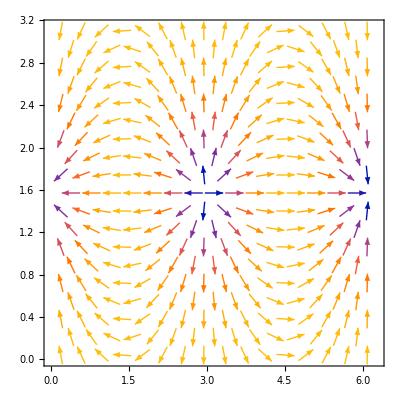
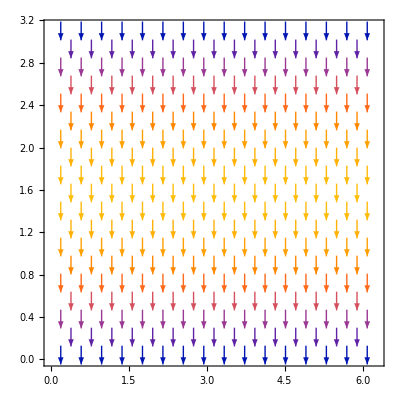
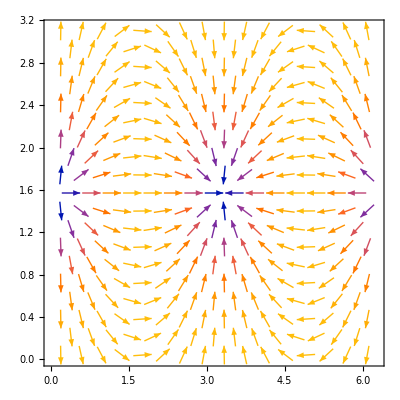

```mathematica
GetDirectivity[l_,m_]:=Module[{eField,bField,poynting,fom},
eField=ElectricField[l,m,{1,0}];
bField=1/(ⅉ)Curl[eField,R,"Spherical"];
poynting=Re@SphericalCrossProduct[eField,Conjugate@bField];
{poynting,eField}
]
PlotDirectivity[poynting_,eField_,l_,m_]:=Module[{fom,field},
fom=Norm[poynting/.{k->2π,r->1}](*,Assumptions->θ∈Reals&&ϕ∈Reals*);
field=Im[FunctionExpand@eField[[2;;]]/.{k->2π,r->1}];
Show[
VectorPlot[{field[[2]],field[[1]]},{ϕ,0,2π},{θ,0,π}](*,*)
(*ContourPlot[fom,{ϕ,0,2π},{θ,0,π},PlotLabel->{l,m},PlotLegends->Automatic,ImageSize->Small,MaxRecursion->1]*)
]
]
Table[Module[{poynting,eField},
{poynting,eField}=GetDirectivity[l,m];
PlotDirectivity[poynting,eField,l,m]],
{l,1,1},{m,-l,l}(*,Method->"CoarsestGrained"*)]
```

```mathematica
formula[l_,m_]:=Simplify@Sqrt[Simplify[ExpToTrig@Total[Abs[FunctionExpand[GetDirectivity[l,m][[1]]]/.{k->2π,r->1}]^2]]]
formula[1,1]
```

(3 √(4 π^6 (3+Cos[2 θ])^2+(1+4 π^2)^2 Sin[θ]^2))/(64 π^5)

```mathematica
PositivePart[x_]:=If[x>=0,x,0];
$Assumptions = x ∈ Reals && y ∈ Reals && z ∈ Reals && r ∈ Reals && r> 0 && θ ∈ Reals && ϕ ∈ Reals && k ∈ Reals && k > 0 && ω > 0;
radius = Sqrt[X . X];
predecessor[α_] := If[α == {0, 0, 0},
   {0, 0, 0},
   Select[
     Table[α - UnitVector[3, j], {j, 1, 3}],
     NonNegative@Min@# &,
     1
     ][[1]]
   ];
firstNonzeroDim[α_] := Position[
     α,
     _?(# > 0 &),
     Infinity, 1
     ][[1]][[1]];
g[α_,direction_] := If[α == {0, 0, 0},
   1/4/π/radius,
   Block[{j, α1, ga},
    α1 = α;
    j = firstNonzeroDim[α];
    α1[[j]] = α1[[j]] - 1;
    ga = g[α1,direction];
    D[ga, X[[j]]] -direction ⅉ k X[[j]]/radius ga // Expand
    ]
   ]
h[α_,direction_,farField_] := Exp[-direction ⅉ k radius] If[farField&&Norm[α,1]>0,
k^Norm[α,1]Coefficient[g[α,direction],k^Norm[α,1]],
g[α,direction]];
μ = k^2/ω^2/ϵ;
c = 1/Sqrt[μ ϵ] // Simplify;
SimplifiedHeaviside[x_] := If[x >= 0, 1, 0];
SafeMoment[CurrentMoment_,α_,dim_]:=If[AllTrue[α,#>=0&],
CurrentMoment[α,dim],
0];
ChargeMoment[α_, CurrentMoment_, dim_,direction_] := -1/(direction ⅉ ω) Sum[If[dim == j,
    α[[j]] SimplifiedHeaviside[α[[j]] - 2] (α[[j]] - 1) SafeMoment[CurrentMoment,(α[[j]] - 2) UnitVector[3, j] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {j }]], j],
    α[[j]] α[[dim]] SimplifiedHeaviside[α[[j]] - 1] SimplifiedHeaviside[α[[dim]] - 1] SafeMoment[CurrentMoment,(α[[j]] - 1) UnitVector[3, j] + (α[[dim]] - 1) UnitVector[3, dim] + Total[α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {dim, j}]], j]
    ],
   {j, 1, 3}]
ElectricMoment[α_, CurrentMoment_, dim_,direction_] :=direction μ ⅉ ω CurrentMoment[α, dim] + 1/ϵ ChargeMoment[α, CurrentMoment, dim,direction]
MagneticMoment[α_,CurrentMoment_, dim_,direction_] := -direction μ Sum[LeviCivitaTensor[3][[dim]][[i]][[j]] SimplifiedHeaviside[α[[i]] - 1] α[[i]] CurrentMoment[(α[[i]] - 1) UnitVector[3, i] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {i}]], j],
   {i, 1, 3}, {j, 1, 3}]
Field[α_, CurrentMoment_, MomentFunction_, dim_,direction_,farField_] := Block[{β},
β=(-1)^Norm[α, 1]/(Times @@ (Factorial/@ α)) MomentFunction[α, CurrentMoment, dim,direction];
If[β===0||β===0.,
0,
β h[α,direction,farField]
]
]
ElectricField[α_, CurrentMoment_, dim_,direction_,farField_] := Field[α, CurrentMoment, ElectricMoment, dim,direction,farField];
MagneticField[α_, CurrentMoment_, dim_,direction_,farField_] := Field[α, CurrentMoment, MagneticMoment, dim,direction,farField];
On[Assert]
CurrentMoment[α_, dim_] := If[α == {0, 0, 0} && dim == 3,
  ⅉ ω p, 0]
EfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,-1,False],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], X -> {r, θ, ϕ}];
BfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim,-1,False],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], X -> {r, θ, ϕ}];
P = {0, 0, p};
n = X/radius;
HJackson = TransformedField["Cartesian" -> "Spherical",
    c k^2/4/π n×P Exp[ⅉ k radius]/radius (1 - 1/ⅉ/k/radius),
    X -> {r, θ, ϕ}] // Simplify;
EJackson = TransformedField["Cartesian" -> "Spherical",
    1/4/π/ϵ Exp[ⅉ k radius] (k^2/radius (n×P)×n + (3 n (n . P) - P) (1/radius^3 - ⅉ k/radius^2)),
    X -> {r, θ, ϕ}] // Simplify;
Assert[Simplify[BfieldThis - HJackson μ] == {0, 0, 0}]
Assert[Simplify[EfieldThis - EJackson] == {0, 0, 0}]
Clear[CurrentMoment, EfieldThis, BfieldThis, P, n, HJackson, EJackson]
```

```mathematica
SolidHarmonic[l_,m_]:=Simplify@TrigExpand@ExpToTrig[TransformedField[
"Spherical"->"Cartesian",r^l SphericalHarmonicY[l,m,θ,ϕ],R->X
]]
ladder[l_,m_,sign_]:=Sqrt[(l-sign m)(l+sign m+1)]SolidHarmonic[l,m+sign]
ladderSpherical[l_,m_,sign_]:=Sqrt[(l-sign m)(l+sign m+1)]SphericalHarmonicY[l,m+sign,θ,ϕ]SphericalHankelH2[l,k r]
Φpoly[l_,m_]:={
1/2(ladder[l,m,1]+ladder[l,m,-1]),
1/(2ⅈ)(ladder[l,m,1]-ladder[l,m,-1]),
-ⅈ ⅈ m SolidHarmonic[l,m]
}
ΦFull[l_,m_]:={
1/2(ladderSpherical[l,m,1]+ladderSpherical[l,m,-1]),
1/(2ⅈ)(ladderSpherical[l,m,1]-ladderSpherical[l,m,-1]),
-ⅈ ⅈ m SphericalHarmonicY[l,m,θ,ϕ]SphericalHankelH2[l,k r]
}
eq[q_]:=If[q==1,
-1/Sqrt[2]{1,ⅉ,0},
If[q==0,
{0,0,1},
1/Sqrt[2]{1,-ⅉ,0}]]
Off[ClebschGordan::tri,ClebschGordan::phy]
(*Varshalovich, 1988. Given J, L=J, J±1, except L=1 for J=0*)
VectorSolidSphericalHarmonic[L_,J_,M_]:=Sum[
ClebschGordan[{L,m},{1,σ},{J,M}]SolidHarmonic[L,m]eq[σ],
{m,-L,L},{σ,-1,1}]//Simplify
ΦVarsha[l_,m_]:=VectorSolidSphericalHarmonic[l,l,m];
ΨVarsha[j_,m_]:=VectorSolidSphericalHarmonic[j-1,j,m];
YVarsha[j_,m_]:=VectorSolidSphericalHarmonic[j+1,j,m];
testEquivalence[l0_,m0_,case_]:=Module[{
azimuthal,allCoefficients,lhs,sol,ξ,poly,CurrentMoment,EfieldCartesian,rn,field,pol,EfieldSpherical
},
poly=If[case==1,
ΦVarsha[l0,m0],
YVarsha[l0,m0]];
(*Echo@poly;*)
Assert[(-ⅈ Exp[ⅉ ϕ] CoordinateTransformData["Spherical"->"Cartesian","OrthonormalBasisRotation"][{r,θ,ϕ}].ΦFull[l0,m0]/.{SphericalHankelH2[l_,x_]:>1}//Simplify//ExpToTrig//TrigExpand//Simplify)==(
Exp[ⅉ ϕ]Φ[l0,m0]/.{SphericalHankelH2[l_,x_]:>1}//Simplify//ExpToTrig//TrigExpand//Simplify)
];
CurrentMoment=Function[{α,dim}, 4π ϵ ⅉ ω(
Lookup[Association[CoefficientRules[poly[[dim]],X]],{α},0][[1]]/((k)^Norm[α, 1]/(Times @@ (Factorial/@ α)))
)];
EfieldCartesian = Simplify[TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,1,False],
      {ax, 0, l0+3}, {ay, 0, l0+3- ax}, {az, 0, l0+3 - ax - ay}],
     {dim, 1, 3}], X -> R]];
rn=1;
pol=If[case==1,{0,1},{1,0}];
EfieldSpherical=ElectricField[l0,m0,pol];
sol=Solve[(Exp[ⅉ k r]EfieldCartesian//ExpToTrig//TrigReduce//Simplify)==const(Exp[ⅉ k r]FunctionExpand@EfieldSpherical//ExpToTrig//Simplify),const]//Simplify;
(*Echo@sol;*)
FreeQ[sol,r|θ|ϕ]&&Length@sol>0
]
```

```mathematica
lMaxVerif=2;
```

Below, we verify that we can write any vector spherical harmonic as a Cartesian solution.

```mathematica
res=Monitor[Table[
{l0,m0,case,res=testEquivalence[l0,m0,case]},
{l0,1,lMaxVerif},{m0,-l0,l0},{case,1,2}
],{l0,m0,case,res}];
Assert[MatchQ[res,{{{{_Integer,_Integer,_Integer,True}..}..}..}]]
```

```mathematica
VectorSolidSphericalHarmonic[1,2,-2]
VectorSolidSphericalHarmonic[1,0,0]
```

{1/4 √(3/π) (x-ⅈ y),-1/4 ⅈ √(3/π) (x-ⅈ y),0}

{-x/(2 √π),-y/(2 √π),-z/(2 √π)}

Now, we verify how we can write any azimuthal solution in terms of Cartesian solution.

```mathematica
Off[ClebschGordan::tri,ClebschGordan::phy]
table=Monitor[Table[{l,m,
res=Solve[VectorSphericalHarmonic[l,l,m]==constant Φpoly[l,m],constant];
res=FreeQ[Simplify@res,X]},
{l,0,lMaxVerif},{m,-l,l}],{l,m,res}];
Assert[MatchQ[table,{{{_Integer,_Integer,True}..}..}]]
```

Now, we turn our attention to the polar part. We know, by construction, that azimuthal part was obtained by the curl of the polar part.
Thus, it is enough to verify that the curl of the vector spherical harmonic gives the polar part.

```mathematica
table=Monitor[Table[{l,m,
sol=Solve[Φpoly[l,m]==const X×ΨVarsha[l,m],const];
res=FreeQ[Simplify@(const/.sol),x|y|z]&&Length@sol>0
},{l,1,lMaxVerif},{m,-l,l}],{l,m,res}];Assert[MatchQ[table,{{{_Integer,_Integer,True}..}..}]]
```

```mathematica
VectorSphericalHarmonic[L_,J_,M_]:=Sum[
ClebschGordan[{L,m},{1,σ},{J,M}]SphericalHarmonicY[L,m,θ,ϕ]eq[σ],
{m,-L,L},{σ,-1,1}]
ToSolid[expr_]:=Simplify@TrigExpand@ExpToTrig[
FunctionExpand@expr/.{
r->Sqrt[X.X],
θ->ArcTan[z,Sqrt[x^2+y^2]],
ϕ->ArcTan[x,y]
}
]
Y1jm[J_,M_]:=ToSolid[r^(J-1)Sqrt[(J+1)/(2J+1)]VectorSphericalHarmonic[J-1,J,M]+r^(J+1)Sqrt[(J)/(2J+1)]VectorSphericalHarmonic[J+1,J,M]]
Ym1jm[J_,M_]:=ToSolid[r^(J-1)Sqrt[(J)/(2J+1)]VectorSphericalHarmonic[J-1,J,M]-r^(J+1)Sqrt[(J+1)/(2J+1)]VectorSphericalHarmonic[J+1,J,M]]
poly=VectorSolidSphericalHarmonic[0,1,0];
(poly+X(X.poly))2 √π//Simplify
4VectorSolidSphericalHarmonic[0,1,0]-Sqrt[2]VectorSolidSphericalHarmonic[2,1,0]
```

{x z,y z,1+z^2}

{(3 x z)/(2 √π),(3 y z)/(2 √π),2/(√π)-(x^2+y^2-2 z^2)/(2 √π)}

```mathematica
VectorSolidSphericalHarmonic[1,0,0]
```

{-x/(2 √π),-y/(2 √π),-z/(2 √π)}

```mathematica
ToCartesian = Transpose@Table[eq[q], {q, -1, 1}];
FromCartesian = Inverse@ToCartesian;
CrossInSCC[a_, b_] := ⅈ Sqrt[2]Table[Sum[
      ClebschGordan[{1, m1}, {1, m2}, {1, m}] a[[m1 + 2]] b[[m2 + 2]],
      {m1, -1, 1}, {m2, -1, 1}], {m, -1, 1}]
X1={x1,y1,z1};
X2={x2,y2,z2};
Assert[Cross[X1,X2]==Simplify[ToCartesian.CrossInSCC[FromCartesian.X1,FromCartesian.X2]]]
rInSCC=FromCartesian.X;
Assert[Simplify[SolidHarmonic[1,1](-2Sqrt[π/3])-rInSCC[[1]]]==0]
Assert[Simplify[SolidHarmonic[1,-1](-2Sqrt[π/3])-rInSCC[[3]]]==0]
Assert[Simplify[SolidHarmonic[1,0](2Sqrt[π/3])-rInSCC[[2]]]==0]
```

```mathematica
l0=3;m0=0;
poly=VectorSphericalHarmonic[l0+1,l0,m0];
poly=ΨVarsha[l0,m0];
(*poly=z(X-{0,0,z})*)
(*poly=eq[-1]*)
(*poly=x X*)
CurrentMoment=Function[{α,dim}, 4π ϵ ⅉ ω(
Lookup[Association[CoefficientRules[poly[[dim]],X]],{α},0][[1]]/((k)^Norm[α, 1]/(Times @@ (Factorial/@ α)))
)];
EfieldCartesian = Simplify[TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,1,False],
      {ax, 0, l0+3}, {ay, 0, l0+3- ax}, {az, 0, l0+3- ax - ay}],
     {dim, 1, 3}], X -> R]]//Simplify
EfieldSpherical=ⅈ ElectricField[l0,m0,{1,0}]//FunctionExpand//Simplify
```

{(ⅇ^(-ⅈ k r) √(21/π) (-15-15 ⅈ k r+6 k^2 r^2+ⅈ k^3 r^3) (3 Cos[θ]+5 Cos[3 θ]))/(8 k^2 r^5),-(ⅇ^(-ⅈ k r) √(21/π) (45+45 ⅈ k r-21 k^2 r^2-6 ⅈ k^3 r^3+k^4 r^4) (Sin[θ]+5 Sin[3 θ]))/(32 k^2 r^5),0}

{(3 ⅇ^(-ⅈ k r) √(7/π) (-15-15 ⅈ k r+6 k^2 r^2+ⅈ k^3 r^3) Cos[θ] (-1+5 Cos[2 θ]))/(2 k^5 r^5),-(3 ⅇ^(-ⅈ k r) √(7/π) (45+45 ⅈ k r-21 k^2 r^2-6 ⅈ k^3 r^3+k^4 r^4) (3+5 Cos[2 θ]) Sin[θ])/(8 k^5 r^5),0}

```mathematica
l0=1;m0=1;
poly=VectorSolidSphericalHarmonic[l0+1,l0,0]
CurrentMoment=Function[{α,dim}, 4π ϵ ⅉ ω(
Lookup[Association[CoefficientRules[poly[[dim]],X]],{α},0][[1]]/((k)^Norm[α, 1]/(Times @@ (Factorial/@ α)))
)];
EfieldCartesian = Simplify[TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,1,False],
      {ax, 0, l0+3}, {ay, 0, l0+3- ax}, {az, 0, l0+3 - ax - ay}],
     {dim, 1, 3}], X -> R]]
```

{-(3 x z)/(2 √(2 π)),-(3 y z)/(2 √(2 π)),(x^2+y^2-2 z^2)/(2 √(2 π))}

{(ⅇ^(-ⅈ k r) (1+ⅈ k r) Cos[θ])/(√(2 π) r^3),(ⅇ^(-ⅈ k r) (1+ⅈ k r-k^2 r^2) Sin[θ])/(2 √(2 π) r^3),0}

```mathematica
poly=VectorSolidSphericalHarmonic[2,1,1]
((-X.X) poly+X(X.poly)//Simplify)/.{x^2+y^2+z^2->1}//Simplify
poly=VectorSolidSphericalHarmonic[0,1,1]
((-X.X) poly+X(X.poly)//Simplify)/.{x^2+y^2+z^2->1}//Simplify
```

{(2 x^2+3 ⅈ x y-y^2-z^2)/(4 √π),-(ⅈ (x^2+3 ⅈ x y-2 y^2+z^2))/(4 √π),(3 (x+ⅈ y) z)/(4 √π)}

{(-ⅈ x^3 y+x^2 (y^2+z^2)-ⅈ x y (y^2+z^2)+(y^2+z^2)^2)/(4 √π),(ⅈ (x^4+ⅈ x^3 y+ⅈ x y (y^2+z^2)+z^2 (y^2+z^2)+x^2 (y^2+2 z^2)))/(4 √π),-((x+ⅈ y) z)/(4 √π)}

{-1/(2 √(2 π)),-ⅈ/(2 √(2 π)),0}

{(-ⅈ x y+y^2+z^2)/(2 √(2 π)),(ⅈ (x^2+ⅈ x y+z^2))/(2 √(2 π)),-((x+ⅈ y) z)/(2 √(2 π))}

```mathematica
fun=Cos[θ];
Table[
{l,m}->Integrate[
fun Conjugate@SphericalHarmonicY[l,m,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}
],{l,0,2},{m,-l,l}]
```

{{{0,0}→0},{{1,-1}→0,{1,0}→2 √(π/3),{1,1}→0},{{2,-2}→0,{2,-1}→0,{2,0}→0,{2,1}→0,{2,2}→0}}

```mathematica
Integrate[Exp[ⅈ ω t],{ω,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ t ω) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(ⅈ t ω)ⅆω

```mathematica
SphericalHarmonicY[0,0,x,y]
```

1/(2 √π)